```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis\\mLI"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
Print["Runs in the list: ",runNum={12681,12684,12687,12688,12689,12690,12691,12692}];(*11159,11369*)
Print["Size: ",runn=Dimensions[runNum][[1]]];
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis\mLI

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: {12681,12684,12687,12688,12689,12690,12691,12692}

Size: 8

```mathematica
metadata1=Table[{},{k,1,Round[runn/2]}];
metadata2=Table[0,{k,1,Round[runn/2]}];
ftdatud=Table[{},{k,1,Round[runn/2]}];
ptdatud=Table[0,{k,1,Round[runn/2]}];
fit1=Table[0,{k,1,Round[runn/2]}];
ftdatudmon=Table[{},{k,1,Round[runn/2]}];
ptdatudmon=Table[0,{k,1,Round[runn/2]}];
fit2=Table[0,{k,1,Round[runn/2]}];
For[i=1,i≤Round[runn/2],i++,
Print["Starting with Run # : ",runNum[[(2i)-1]]," & ",runNum[[(2i)]]];
metadata1[[i]]=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[(2i)-1]],10,6],"\\",IntegerString[runNum[[(2i)-1]],10,6],"_Meta3.edm"],metaStructure2];
metadata2[[i]]=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[(2i)]],10,6],"\\",IntegerString[runNum[[(2i)]],10,6],"_Meta3.edm"],metaStructure2];
maxCy=metadata1[[i]][[-1]][[2]];
(*UD*)
Print["Fit1:UD"];
tab=Table[{55+(k-1)*25,{(metadata1[[i]][[k]][[27]]+metadata1[[i]][[k]][[28]])/1000,8(Sqrt[metadata1[[i]][[k]][[27]]]+Sqrt[metadata1[[i]][[k]][[28]]])/1000}},{k,1,maxCy}];
ptdatud[[i]]=AppendTo[tab,{380,{(metadata2[[i]][[1]][[27]]+metadata2[[i]][[1]][[28]])/1000,8(Sqrt[metadata2[[i]][[1]][[27]]]+Sqrt[metadata2[[i]][[1]][[28]]])/1000}}];
If[i==2,ptdatud[[i]]=Delete[ptdatud[[i]],4]];
If[i==3,ptdatud[[i]]=Delete[ptdatud[[i]],3]];
ftdatud[[i]]=Transpose[{ptdatud[[i]][[;;,1]],ptdatud[[i]][[;;,2]][[;;,1]]}];
Print[fit1[[i]]=NonlinearModelFit[ftdatud[[i]],(bb Exp[cc t]+dd Exp[ee t]+aa),{{aa,1},{bb,10},{cc,-.1},{dd,10},{ee,-.1}},t,Method->NMinimize]];
(*UD/Mon*)
Print["Fit2:UD/Mon"];
tab2=Table[{55+(k-1)*25,{(metadata1[[i]][[k]][[27]]+metadata1[[i]][[k]][[28]])/metadata1[[i]][[k]][[30]],8(Sqrt[metadata1[[i]][[k]][[27]]]+Sqrt[metadata1[[i]][[k]][[28]]])/metadata1[[i]][[k]][[30]]}},{k,1,maxCy}];
ptdatudmon[[i]]=AppendTo[tab2,{380,{(metadata2[[i]][[1]][[27]]+metadata2[[i]][[1]][[28]])/metadata2[[i]][[1]][[30]],8(Sqrt[metadata2[[i]][[1]][[27]]]+Sqrt[metadata2[[i]][[1]][[28]]])/metadata2[[i]][[1]][[30]]}}];
If[i==2,ptdatudmon[[i]]=Delete[ptdatudmon[[i]],4]];
If[i==3,ptdatudmon[[i]]=Delete[ptdatudmon[[i]],3]];
ftdatudmon[[i]]=Transpose[{ptdatudmon[[i]][[;;,1]],ptdatudmon[[i]][[;;,2]][[;;,1]]}];
Print[fit2[[i]]=NonlinearModelFit[ftdatudmon[[i]],(bb Exp[cc t]+dd Exp[ee t]+aa),{{aa,1},{bb,10},{cc,-.1},{dd,10},{ee,-.1}},t,Method->NMinimize]];
Print["---"];
];
(*
{aa,bb,cc,dd,ee};
{{aa,1},{bb,1},{cc,-1},{dd,1},{ee,-1}}
*)
```

Starting with Run # : 12681 & 12684

Fit1:UD

FittedModel[1.32355+173.412 ⅇ^(-1.03538 t)+16.4029 ⅇ^(-0.00603346 t)]

Fit2:UD/Mon

FittedModel[0.00622475+27.65 ⅇ^(-0.697654 t)+0.0759593 ⅇ^(-0.00619004 t)]

---

Starting with Run # : 12687 & 12688

Fit1:UD

FittedModel[10.8416-13.6656 ⅇ^(-2.15553 t)+91.8044 ⅇ^(-0.0105479 t)]

Fit2:UD/Mon

FittedModel[0.00972756-6.17056 ⅇ^(-0.497426 t)+0.0960547 ⅇ^(-0.00758587 t)]

---

Starting with Run # : 12689 & 12690

Fit1:UD

FittedModel[7.26364+28.4414 ⅇ^(-4.65532 t)+79.8589 ⅇ^(-0.00729495 t)]

Fit2:UD/Mon

FittedModel[0.00840625+29.5281 ⅇ^(-1.33283 t)+0.0894173 ⅇ^(-0.00657063 t)]

---

Starting with Run # : 12691 & 12692

Fit1:UD

FittedModel[5.0024+517.598 ⅇ^(-1.42655 t)+72.3616 ⅇ^(-0.0061986 t)]

Fit2:UD/Mon

FittedModel[0.0122227+6.07127 ⅇ^(-1.01924 t)+0.0957033 ⅇ^(-0.0082354 t)]

---

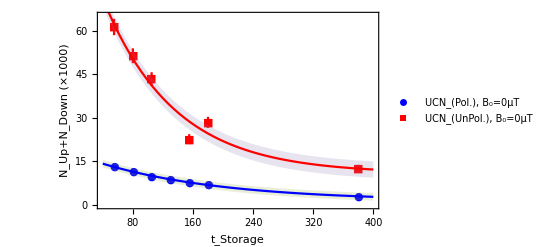

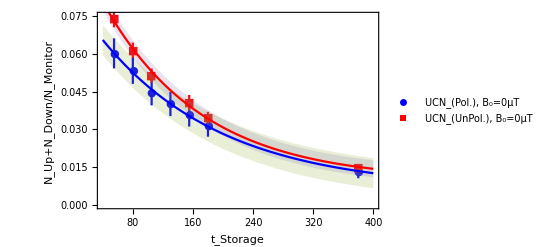

```mathematica
Show[{
EDAListPlot[ptdatud[[1]],ptdatud[[2]],PlotLegends->{"UCN_(Pol.), B_0=0μT","UCN_(UnPol.), B_0=0μT"},PlotRange->{{40,400},{0,65}},PlotStyle->{Blue,Red,Gray,Green},Frame->True,FrameLabel->{"t_Storage","N_Up+N_Down (×1000)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[{fit1[[1]][t],fit1[[2]][t],fit1[[1]][t]+ptdatud[[1]][[1]][[2]][[2]],fit1[[1]][t]-ptdatud[[1]][[1]][[2]][[2]],fit1[[2]][t]+ptdatud[[2]][[1]][[2]][[2]],fit1[[2]][t]-ptdatud[[2]][[1]][[2]][[2]]},{t,40,400},Filling->{{3->{4}},{5->{6}}},PlotStyle->{Blue,Red,None,None,None,None},PlotRange->Full,Frame->True,FrameLabel->{"t_filling","N_Up+N_Down"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
Show[{
EDAListPlot[ptdatudmon[[1]],ptdatudmon[[2]],PlotLegends->{"UCN_(Pol.), B_0=0μT","UCN_(UnPol.), B_0=0μT"},PlotRange->{{40,400},{0,0.075}},PlotStyle->{Blue,Red,Gray,Green},Frame->True,FrameLabel->{"t_Storage","N_Up+N_Down/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[{fit2[[1]][t],fit2[[2]][t],fit2[[1]][t]+ptdatudmon[[1]][[1]][[2]][[2]],fit2[[1]][t]-ptdatudmon[[1]][[1]][[2]][[2]],fit2[[2]][t]+ptdatudmon[[2]][[1]][[2]][[2]],fit2[[2]][t]-ptdatudmon[[2]][[1]][[2]][[2]]},{t,40,400},Filling->{{3->{4}},{5->{6}}},PlotStyle->{Blue,Red,None,None,None,None},PlotRange->Full,Frame->True,FrameLabel->{"t_filling","N_Up+N_Down"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
```

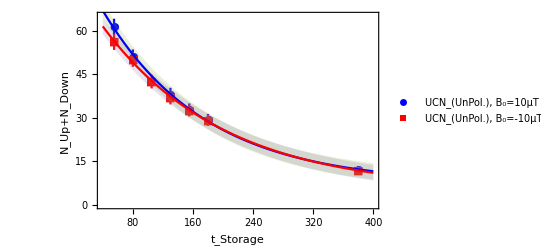

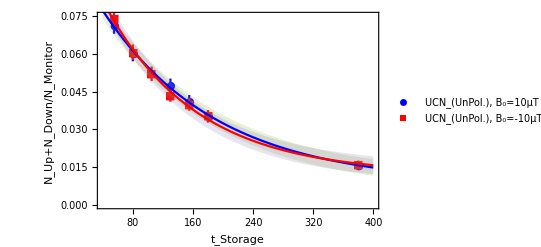

```mathematica
Show[{
EDAListPlot[ptdatud[[3]],ptdatud[[4]],PlotLegends->{"UCN_(UnPol.), B_0=10μT","UCN_(UnPol.), B_0=-10μT"},PlotRange->{{40,400},{0,65}},PlotStyle->{Blue,Red,Gray,Green},Frame->True,FrameLabel->{"t_Storage","N_Up+N_Down"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[{fit1[[3]][t],fit1[[4]][t],fit1[[3]][t]+ptdatud[[3]][[1]][[2]][[2]],fit1[[3]][t]-ptdatud[[3]][[1]][[2]][[2]],fit1[[4]][t]+ptdatud[[4]][[1]][[2]][[2]],fit1[[4]][t]-ptdatud[[4]][[1]][[2]][[2]]},{t,40,400},Filling->{{3->{4}},{5->{6}}},PlotStyle->{Blue,Red,None,None,None,None},PlotRange->Full,Frame->True,FrameLabel->{"t_filling","N_Up+N_Down"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
Show[{
EDAListPlot[ptdatudmon[[3]],ptdatudmon[[4]],PlotLegends->{"UCN_(UnPol.), B_0=10μT","UCN_(UnPol.), B_0=-10μT"},PlotRange->{{40,400},{0,0.075}},PlotStyle->{Blue,Red,Gray,Green},Frame->True,FrameLabel->{"t_Storage","N_Up+N_Down/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[{fit2[[3]][t],fit2[[4]][t],fit2[[3]][t]+ptdatudmon[[3]][[1]][[2]][[2]],fit2[[3]][t]-ptdatudmon[[3]][[1]][[2]][[2]],fit2[[4]][t]+ptdatudmon[[4]][[1]][[2]][[2]],fit2[[4]][t]-ptdatudmon[[4]][[1]][[2]][[2]]},{t,40,400},Filling->{{3->{4}},{5->{6}}},PlotStyle->{Blue,Red,None,None,None,None},PlotRange->Full,Frame->True,FrameLabel->{"t_filling","N_Up+N_Down"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
```

```mathematica
aaa={{1,1},{2,2},{3,3}};
Delete[aaa,2]
```

{{1,1},{3,3}}

```mathematica
ptdatud[[1]]
ptdatud[[2]]
ptdatud[[3]]
ptdatud[[4]]
```

{{55,{13.095,1.29467}},{80,{11.545,1.13315}},{105,{9.824,1.11941}},{130,{8.877,1.06565}},{155,{7.791,0.998358}},{180,{6.879,0.938335}},{380,{2.971,0.616609}}}

{{55,{61.255,2.79998}},{80,{51.367,2.56399}},{105,{43.334,2.35503}},{155,{22.644,1.70223}},{180,{28.419,1.90714}},{380,{12.552,1.26734}}}

{{55,{61.297,2.80089}},{80,{50.977,2.55425}},{130,{38.129,2.20908}},{155,{32.884,2.0516}},{180,{29.399,1.93967}},{380,{12.103,1.24462}}}

{{55,{56.048,2.67826}},{80,{50.083,2.53181}},{105,{42.453,2.33087}},{130,{36.784,2.16973}},{155,{32.504,2.03956}},{180,{29.158,1.93167}},{380,{11.843,1.23116}}}

{{55,{1.8711,0.0855281}},{80,{1.77971,0.0888345}},{105,{1.76441,0.0958888}},{155,{1.16257,0.0873948}},{180,{1.65251,0.110896}},{380,{1.68994,0.170627}}}

{{55,{1.87238,0.0855561}},{80,{1.7662,0.0884971}},{130,{1.7181,0.0995417}},{155,{1.68831,0.105332}},{180,{1.70949,0.112788}},{380,{1.62949,0.167569}}}

{{55,{1.71204,0.0818103}},{80,{1.73523,0.0877197}},{105,{1.72854,0.0949049}},{130,{1.6575,0.0977686}},{155,{1.6688,0.104714}},{180,{1.69548,0.112323}},{380,{1.59448,0.165757}}}

1.65337

1.73066

1.68458

0.252158

0.0824419

0.0491112

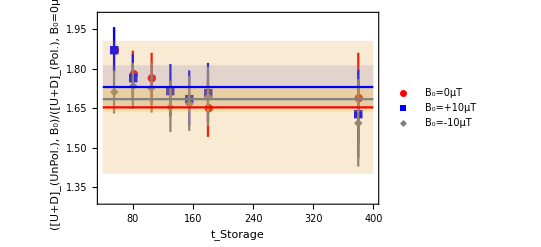

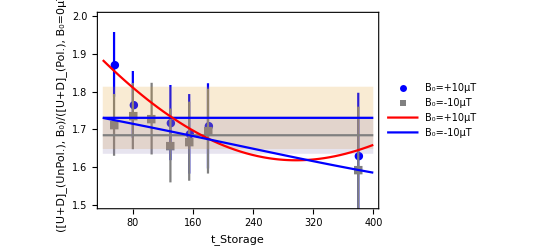

```mathematica
ptratpolun1={
{ptdatud[[2]][[1]][[1]],{ptdatud[[2]][[1]][[2]][[1]]/(2.5ptdatud[[1]][[1]][[2]][[1]]),ptdatud[[2]][[1]][[2]][[2]]/(2.5ptdatud[[1]][[1]][[2]][[1]])}},
{ptdatud[[2]][[2]][[1]],{ptdatud[[2]][[2]][[2]][[1]]/(2.5ptdatud[[1]][[2]][[2]][[1]]),ptdatud[[2]][[2]][[2]][[2]]/(2.5ptdatud[[1]][[2]][[2]][[1]])}},
{ptdatud[[2]][[3]][[1]],{ptdatud[[2]][[3]][[2]][[1]]/(2.5ptdatud[[1]][[3]][[2]][[1]]),ptdatud[[2]][[3]][[2]][[2]]/(2.5ptdatud[[1]][[3]][[2]][[1]])}},
{ptdatud[[2]][[4]][[1]],{ptdatud[[2]][[4]][[2]][[1]]/(2.5ptdatud[[1]][[5]][[2]][[1]]),ptdatud[[2]][[4]][[2]][[2]]/(2.5ptdatud[[1]][[5]][[2]][[1]])}},
{ptdatud[[2]][[5]][[1]],{ptdatud[[2]][[5]][[2]][[1]]/(2.5ptdatud[[1]][[6]][[2]][[1]]),ptdatud[[2]][[5]][[2]][[2]]/(2.5ptdatud[[1]][[6]][[2]][[1]])}},
{ptdatud[[2]][[6]][[1]],{ptdatud[[2]][[6]][[2]][[1]]/(2.5ptdatud[[1]][[7]][[2]][[1]]),ptdatud[[2]][[6]][[2]][[2]]/(2.5ptdatud[[1]][[7]][[2]][[1]])}}
}
ptratpolun2={
{ptdatud[[3]][[1]][[1]],{ptdatud[[3]][[1]][[2]][[1]]/(2.5ptdatud[[1]][[1]][[2]][[1]]),ptdatud[[3]][[1]][[2]][[2]]/(2.5ptdatud[[1]][[1]][[2]][[1]])}},
{ptdatud[[3]][[2]][[1]],{ptdatud[[3]][[2]][[2]][[1]]/(2.5ptdatud[[1]][[2]][[2]][[1]]),ptdatud[[3]][[2]][[2]][[2]]/(2.5ptdatud[[1]][[2]][[2]][[1]])}},
{ptdatud[[3]][[3]][[1]],{ptdatud[[3]][[3]][[2]][[1]]/(2.5ptdatud[[1]][[4]][[2]][[1]]),ptdatud[[3]][[3]][[2]][[2]]/(2.5ptdatud[[1]][[4]][[2]][[1]])}},
{ptdatud[[3]][[4]][[1]],{ptdatud[[3]][[4]][[2]][[1]]/(2.5ptdatud[[1]][[5]][[2]][[1]]),ptdatud[[3]][[4]][[2]][[2]]/(2.5ptdatud[[1]][[5]][[2]][[1]])}},
{ptdatud[[3]][[5]][[1]],{ptdatud[[3]][[5]][[2]][[1]]/(2.5ptdatud[[1]][[6]][[2]][[1]]),ptdatud[[3]][[5]][[2]][[2]]/(2.5ptdatud[[1]][[6]][[2]][[1]])}},
{ptdatud[[3]][[6]][[1]],{ptdatud[[3]][[6]][[2]][[1]]/(2.5ptdatud[[1]][[7]][[2]][[1]]),ptdatud[[3]][[6]][[2]][[2]]/(2.5ptdatud[[1]][[7]][[2]][[1]])}}
}
ptratpolun3=Table[{ptdatud[[4]][[k]][[1]],{ptdatud[[4]][[k]][[2]][[1]]/(2.5ptdatud[[1]][[k]][[2]][[1]]),ptdatud[[4]][[k]][[2]][[2]]/(2.5ptdatud[[1]][[k]][[2]][[1]])}},{k,1,7}]
mu1=Mean[ptratpolun1[[;;,2]][[;;,1]]]
mu2=Mean[ptratpolun2[[;;,2]][[;;,1]]]
mu3=Mean[ptratpolun3[[;;,2]][[;;,1]]]
sig1=StandardDeviation[ptratpolun1[[;;,2]][[;;,1]]]
sig2=StandardDeviation[ptratpolun2[[;;,2]][[;;,1]]]
sig3=StandardDeviation[ptratpolun3[[;;,2]][[;;,1]]]
Show[{EDAListPlot[ptratpolun1,ptratpolun2,ptratpolun3,PlotRange->{{040,400},{1.3,2.}},PlotLegends->{"B_0=0μT","B_0=+10μT","B_0=-10μT"},PlotStyle->{Red,Blue,Gray},Frame->True,FrameLabel->{"t_Storage","([U+D]_(UnPol.), B_0)/([U+D]_(Pol.), B_0=0μT)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[{mu1,mu1-sig1,mu1+sig1,mu2,mu2-sig2,mu2+sig2,mu3,mu3-sig3,mu3+sig3},{t,40,400},Filling->{{2->{3}},{5->{6}},{8->{9}}},PlotStyle->{Red,None,None,Blue,None,None,Gray,None,None},Frame->True,FrameLabel->{"t_Storage","([U+D]_(UnPol.), B_0)/([U+D]_(Pol.), B_0=0μT)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}],
Plot[{fit1[[2]][t]/(fit1[[1]][t]),fit1[[3]][t]/(fit1[[1]][t]),fit1[[4]][t]/(fit1[[1]][t])},{t,40,400},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Gray,Dashed}},Frame->True,FrameLabel->{"t_Storage","([U+D]_(UnPol.), B_0)/([U+D]_(Pol.), B_0=0μT)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
Show[{EDAListPlot[ptratpolun2,ptratpolun3,PlotRange->{{040,400},{1.5,2.}},PlotLegends->{"B_0=+10μT","B_0=-10μT"},PlotStyle->{Blue,Gray},Frame->True,FrameLabel->{"t_Storage","([U+D]_(UnPol.), B_0)/([U+D]_(Pol.), B_0=0μT)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium}],
Plot[{mu2,mu2-sig2,mu2+sig2,mu3,mu3-sig3,mu3+sig3},{t,40,400},Filling->{{2->{3}},{5->{6}},{8->{9}}},PlotStyle->{Blue,None,None,Gray,None,None},Frame->True,FrameLabel->{"t_Storage","([U+D]_(UnPol.), B_0)/([U+D]_(Pol.), B_0=0μT)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}],
Plot[{fit1[[3]][t]/(2.5fit1[[1]][t]),fit1[[4]][t]/(2.5fit1[[1]][t])},{t,40,400},PlotLegends->{"B_0=+10μT","B_0=-10μT"},PlotStyle->{Red,Blue,Gray},Frame->True,FrameLabel->{"t_Storage","([U+D]_(UnPol.), B_0)/([U+D]_(Pol.), B_0=0μT)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
}]
```

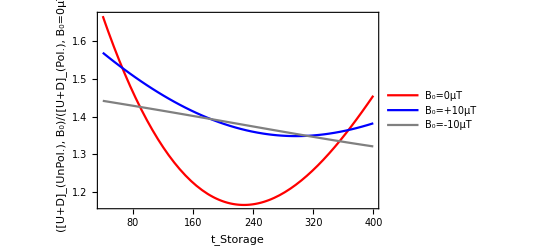

```mathematica
Plot[{fit1[[2]][t]/(3fit1[[1]][t]),fit1[[3]][t]/(3fit1[[1]][t]),fit1[[4]][t]/(3fit1[[1]][t])},{t,40,400},PlotLegends->{"B_0=0μT","B_0=+10μT","B_0=-10μT"},PlotStyle->{Red,Blue,Gray},Frame->True,FrameLabel->{"t_Storage","([U+D]_(UnPol.), B_0)/([U+D]_(Pol.), B_0=0μT)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{28,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000}]
```